```mathematica
vertfunc = Function[{pos,val,blah},Rectangle[pos-#/45,pos+#/45]&@(Subtract@@(Reverse@MinMax[#])&/@Transpose[Ramp[val[[-1]]]])];
```

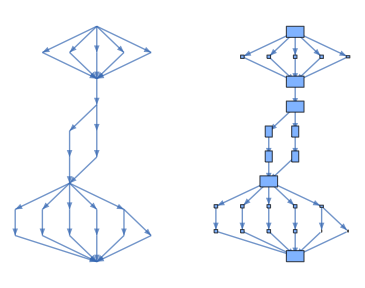
-Graphics--Graphics-

```mathematica
Row[
MapIndexed[Framed[GraphicsRow[#, Spacings->If[First[#2]==1, 30, {{2-> 15, 3->15}, 3}]], FrameStyle->LightGray]&,Partition[Join[{{{"[◼]", "PatternsLayeredGraph"}}[ResourceData["LifeWiki Dataset 2025"]["Worker bee"],Automatic,"VertexSizeFunction":>(7 Sqrt[Dimensions[#]]&), ImageSize->{Automatic, 275}],{{"[◼]", "BoundingBoxLayeredGraph"}}[ResourceData["LifeWiki Dataset 2025"]["Worker bee"], Automatic, ImageSize->{Automatic, 275}, VertexShapeFunction->vertfunc]},
{{{"[◼]", "PatternsLayeredGraph"}}[ResourceData["LifeWiki Dataset 2025"]["29P9"],Automatic,"VertexSizeFunction":>(7 Sqrt[Dimensions[#]]&), ImageSize->{Automatic, 275}, PlotRangePadding->{0, 0}],{{"[◼]", "BoundingBoxLayeredGraph"}}[ResourceData["LifeWiki Dataset 2025"]["29P9"], Automatic, ImageSize->{Automatic, 275}, EdgeShapeFunction->"Arrow"]}
], 2]], Spacer[25]]
```

```mathematica
vertfunc = Function[{pos,val,blah},Rectangle[pos-#/45,pos+#/45]&@(Subtract@@(Reverse@MinMax[#])&/@Transpose[Ramp[val[[-1]]]])];
```

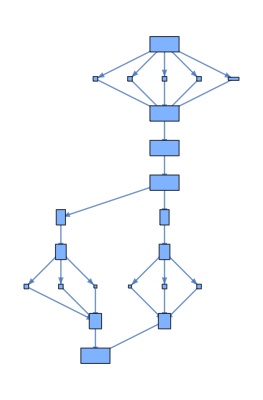
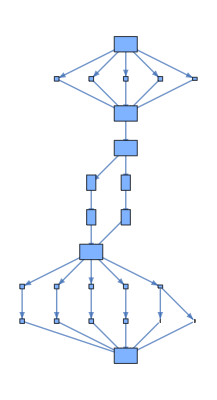
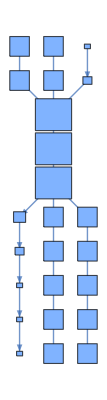
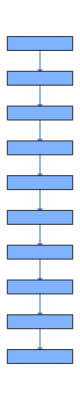
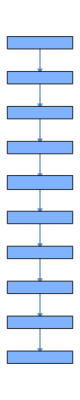
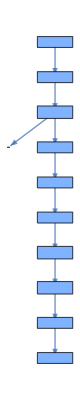
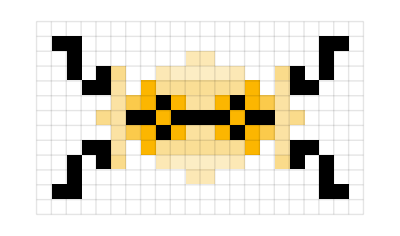
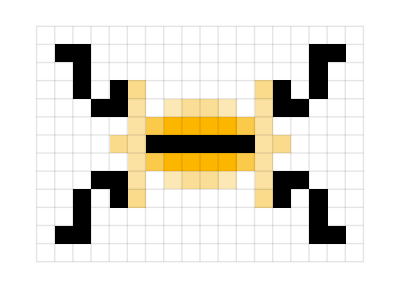
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
1972 | 1972 | 1984 | 1997 | 1998 | 2014-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
2018 | 2020 | 2021 | 2022 | 2023

```mathematica
Style[Row[With[{elems=With[{data=Select[ResourceData["LifeWiki Dataset 2025"],#Class === "Oscillator" && #Period ==9&]},MapIndexed[{Graph[{{"[◼]", "BoundingBoxLayeredGraph"}}[#, Automatic, VertexShapeFunction->vertfunc],ImageSize->{Automatic,130}],{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{#MatrixData,0},9,ImageSize->13Sqrt[Reverse@Dimensions[#1["MatrixData"]]]],Text[Style[#Year,Small,GrayLevel[0.25]]]}&,Values[SortBy[data//Quiet,#Year&]]]]},Grid[Transpose[#],Dividers->{All,False},FrameStyle->GrayLevel[.7],Alignment->Center]&/@Partition[elems, UpTo[6]]]],LineSpacing->{1,40}]
```